```mathematica
(* M-B:f(u)=4π(M/(2πRT))^(3/2)u^2 e^(-Mu^2/2RT)
<u>=∫_0^∞ uf(u)ⅆu=(8RT/πM)^(1/2)
Subscript[u, rms]=<u^2>^1/2=(3RT/M)^1/2
prob. u is b/w u1 and u2: p(u1≤u≤u2)=∫_u1^u2 f(u)ⅆu
H-atom 1s orbital:
prob. that e- is within a0 of the nuleus
=∫_0^a0 r^2(|Subscript[R, 1σ](r)|)^2 ⅆr
 *)
f[u_]:=4*Pi*(m/(2*Pi*r*t))^(3/2)*u^2*E^(-m*u^2/(2*r*t));
```

```mathematica
uavg=Assuming[{m>0,r>0,t>0},Integrate[u*f[u],{u,0,Infinity}]]
```

2 √(2/π) √((r t)/m)

```mathematica
urms=Sqrt[Assuming[{m>0,r>0,t>0},Integrate[(u^2*f[u]),{u,0,Infinity}]]]
```

√3 √((r t)/m)

```mathematica
r=8.314;t=300;m=0.028;
urms
```

516.948

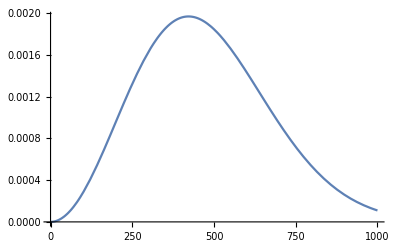

```mathematica
Plot[f[u],{u,0,1000}]
```

```mathematica
Assuming[{m>0,r>0,t>0},Integrate[f[u],{u,300,500}]]
```

0.37632

```mathematica
Clear[r];
```

```mathematica
f[r_]:=2*(1/a0)^(3/2)*E^(-r/a0);
```

```mathematica
prob=Integrate[r^2*f[r]^2,{r,0,a0}]
```

1-5/ⅇ^2

```mathematica
N[%]
```

0.323324

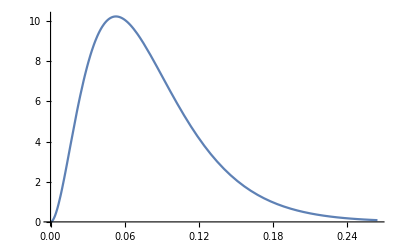

```mathematica
a0=0.0529;
Plot[r^2*f[r]^2,{r,0,5*a0}]
```